```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

#### Load in Suave

```mathematica
Install["Suave-Linux"];
Install["Vegas-Linux"];
Install["Divonne-Linux"];
```

## Global Constants

```mathematica
TEMP = 9.*^-9; (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
hbarc = (0.1973269788*1.*^-3); (* GeV fm *)
```

## Interpolating Functions

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = nb*Yn;
nd          = Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-1*)

ndFreeList =(2.*NM*muList)^1.5/(3.*π^2*hbarc^3);
ndCorrectedList = (ndList*ndList)/ndFreeList;
ndCorrected = Interpolation[Transpose[{radius, ndCorrectedList}]];

NSMass = Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *)
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

## Useful Functions

```mathematica
EscVelSetUp[rad_?NumericQ] := Module[                                                           (* escape velocity inside star, in natural units *)
{GravPot,r}, 
GravPot =NIntegrate[(2.*G*NSMass[r]*2.*^30)/(r^2*1.*^3), {r, rad, rMax}];
Sqrt[GravPot +(2.*G*NSMass[rMax]*2.*^30)/(rMax*1.*^3)]/SOL
]; 


EscVel = Interpolation[Table[{ri, EscVelSetUp[ri]}, {ri, rMin, Last[radius]}]];

(*================================================================================================================================================================*)


FermiDirac[s_, t_, vel_ , chempot_,MU_]:= Module[                               (* vel can be to be interchanged for initial and final velocities *)
{MUP, argument},
MUP = (MU+1.)/2.;
argument = (1/TEMP(0.5*NM*(2.*MU*MUP*t^2 +2.*MUP*s^2-MU*vel^2)- chempot));
Which[(argument > 600.), 0., argument<-600., 1., True,
	1./(1. + Exp[argument])]
]; 

(*================================================================================================================================================================*)

PreFacs[MU_]:= Module[
{ MUP},

MUP = (MU + 1.)/2.; 
(64*π*MUP^4*Erf[((Sqrt[(3./2.)]*NSVEL)/VELDISP)]*1.*^54)/(NSVEL*MU*NM*SOL^3)
];

(*================================================================================================================================================================*)

plotFD[MU_, r_] :=Manipulate[

w             =EscVel[r];
Module[{w =w, chempot, FVSqr, MUP, tu, su, s, t, v},

MUP = (MU + 1.)/2.;

chempot = muFn[r]*1.*^-3;
FVSqr = (2.*chempot)/NM;
tu =1.05*Sqrt[(FVSqr + MU*w^2)/(2.*MU * MUP)];
su = 1.05*Sqrt[(FVSqr + MU*w^2)/(2.*MUP)];

RegionPlot[a*x*FermiDirac[y, x, w , chempot,MU]*(1.-FermiDirac[y, x, a*w , chempot,MU])*UnitStep[x+y-w]*UnitStep[a*w-Abs[x-y]]>0, {x, 0, tu}, {y, 0, su}]
],{a, 0, 1}];
```

```mathematica
plotFD[1., 1.]
```

## Define (s, t, v) Integrand

```mathematica
OmegaIntegrand[s_, t_, v_, w_, chempot_, dm_ ] := v*t*FermiDirac[s, t, w, chempot, dm]*(1. - FermiDirac[s, t, v, chempot, dm]);
```

## Do the integrals

```mathematica
dCdV[r_,MU_] := Module[
{w, chempot, FVSqr, MUP, tub, sub, s, t, v},

MUP = (MU + 1.)/2.;

w             =EscVel[r];
chempot = muFn[r]*1.*^-3;
FVSqr = (2.*chempot)/NM;


tub =1.05*Sqrt[(FVSqr + MU*w^2)/(2.*MU * MUP)];
sub = 1.05*Sqrt[(FVSqr + MU*w^2)/(2.*MUP)];


(Suave[OmegaIntegrand[s, t, v,w, chempot, MU], {v, 0, w}, {s, 0, sub}, {t, 0, tub},AccuracyGoal->6, MaxPoints->500000, Verbose->0][[1,1]])
];
```

```mathematica
CperVList = Table[{x,dCdV[x, 1.*^-2]},{x, rMin, 11.5, ((11.5-rMin)/(20-1))}];
CperV = Interpolation[CperVList];
```

Suave::accuracy: Desired accuracy was not reached within 500000 function evaluations on 500 subregions.

General::stop: Further output of Suave::accuracy will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/home/student.unimelb.edu.au/mvirgato/Documents/Project/Masters/cap_rate/Mathematica_cap/Suave-Linux',1011,7].

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

LinkObject::linkn: Argument LinkObject['/home/student.unimelb.edu.au/mvirgato/Documents/Project/Masters/cap_rate/Mathematica_cap/Suave-Linux',1011,7] in LinkWrite[LinkObject['/home/student.unimelb.edu.au/mvirgato/Documents/Project/Masters/cap_rate/Mathematica_cap/Suave-Linux',1011,7],CallPacket[0,{3,1,0.001,1.×10^-6,4,0,0,500000,1000,2,50,}]] has an invalid LinkObject number; the link may be closed.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

LinkObject::linkn: Argument LinkObject['/home/student.unimelb.edu.au/mvirgato/Documents/Project/Masters/cap_rate/Mathematica_cap/Suave-Linux',1011,7] in LinkWrite[LinkObject['/home/student.unimelb.edu.au/mvirgato/Documents/Project/Masters/cap_rate/Mathematica_cap/Suave-Linux',1011,7],CallPacket[0,{3,1,0.001,1.×10^-6,4,0,0,500000,1000,2,50,}]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of LinkObject::linkn will be suppressed during this calculation.

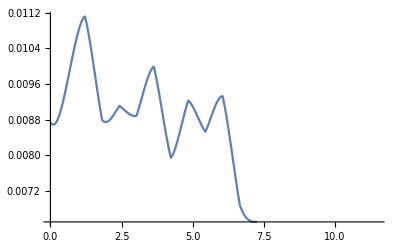

```mathematica
Plot[CperV[x], {x, rMin, 11.5}, PlotRange->Full]
```

## Radius Integrand

## Integrating over semi-infinite domain example

```mathematica
(*
f[tx_, ty_, dm_] := Module[{x, y, jacobian},
x = tx/(1-tx);
y = ty/(1-ty);
jacobian = 1/(1-tx)^2*1/(1-ty)^2;
Exp[-x^2-y^2]*jacobian*dm
];
*)
```